## Model

### Variables

```mathematica
(*B0 to be determined with regression.*)
R =  0.02; (*Tube radius (m).*)
z1 = 0.0402; (*Distance from first wire loop (m).*)
l = 0.0543; (*Length of solenoid (m).*)
g = 9.8; (*Gravitational acceleration (m/s^2)*)
NT = 397;(*Number of wire turns.*)
```

### Old model

```mathematica
(*We'll remove the constant we are looking to fit (B0) from the field.*)
NormalizedField[z_] := R^3/(R^2+z^2)^(3/2);

(*AccelField[t_] := Composition[Field, AccelMotion][t]*)
(*AccelVoltage[t_] := -NT Pi R^2 AccelField'[t]*)
```

### New Model

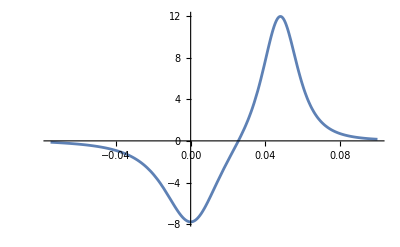

```mathematica
n = 100; (*Number of divisions.*)
z[k_] := z1 + (k-1)l/(n-1) (*Fall distance for each loop.*)
h[t_, k_] := z[k] - g t^2/2  (*Height with respect to z[k] at a given time.*)
AccelField[t_, k_] := Composition[NormalizedField, h][t, k]
AccelVoltage[t_] = -NT Pi R^2 Sum[D[AccelField[t, k]/n, t], {k, 1, n}];

minimumTime = t/.FindMinimum[AccelVoltage[t], {t, 0.05}][[-1]]; (*Time of second minimum.*)

(*Shifting voltage so as to have minimumTime = 0*)
AccelVoltage[t_] = AccelVoltage[t+minimumTime];

Plot[AccelField[t+minimumTime, 20]/n, {t, -1, 1}, PlotRange->All];
Plot[AccelVoltage[t], {t, -0.075, 0.1}, PlotRange->All]
```

## Data

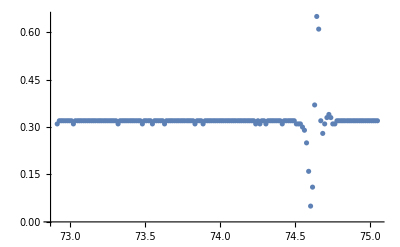

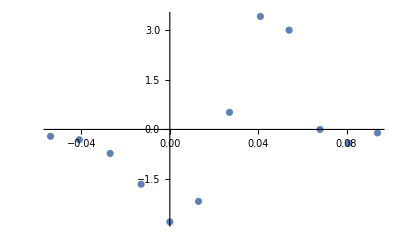

```mathematica
notePath = NotebookDirectory[];
fileName = "inputData\\big_magnet\\397_G_NO_REKT_5.txt";
fullName = StringJoin[{notePath, "\\", fileName}];
data = Import[fullName, "Data"][[5;;-2]];
ListPlot[data]
heightShift = 3.3 / 0.32;
data = MapAt[heightShift# - 3.3&, data, {All,2}];

(*We'll shift the data so as to have the first minimum at t = 0.*)
positionOfMinimum = Position[data[[All, 2]], Min[data[[All, 2]]]][[1, 1]];
timeOfMinimum = data[[positionOfMinimum, 1]];

data = MapAt[# - timeOfMinimum &, data, {All, 1}];

(*We filter the data points whose voltage is outside an interval away from zero.*)
data = Select[data,-0.06<#[[1]] <0.1 &][[;;-1]];
dataPlot = ListPlot[data, PlotRange->All]
```

## Fitting

$3564.59\pm244.607$

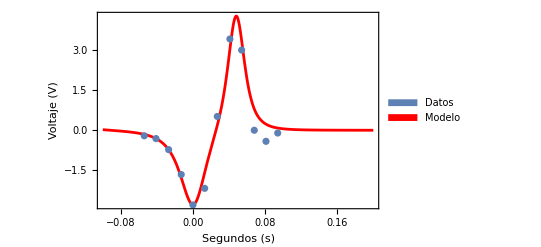

C:\Users\Lenovo\Documents\GitHub\electromotive-voltage\EV analysis\graphics\big_magnet\new_model_big_magnet_5.jpg

```mathematica
(*We bring back the constant B0. So AccelVoltage is no longer normalized*)

AbnormalAccelVoltage[t_] = B0 AccelVoltage[t];

fitModel = NonlinearModelFit[data, AbnormalAccelVoltage[t], B0, t];fitPlot = Plot[fitModel[t], {t, -0.1, 0.2}, PlotStyle->Red, PlotRange->All];

(*accelPlot = Plot[AccelVoltage[t], {t,-0.1, 0.1}, PlotStyle->Green , PlotRange->All];*)

(*Parameters converted from tesla to gauss*)
B0Fitted = 10000 B0/.fitModel["BestFitParameters"];
standardError = 10000 fitModel["ParameterErrors"][[1]];

StringJoin[{"$", ToString[B0Fitted],"\\pm",ToString[standardError], "$"}]

fullPlot = Show[fitPlot, dataPlot, Frame->True, FrameLabel->{"Segundos (s)", "Voltaje (V)"}, LabelStyle->Directive[FontFamily->"Times New Roman", FontColor->Black, FontSize->14]];

fullPlot = Legended[fullPlot, Placed[SwatchLegend[{RGBColor["#5E81B5"], Red}, {"Datos", "Modelo"}, LabelStyle->{FontFamily->"Times New Roman", FontSize->12}, LegendFunction->Panel], {0.87, 0.84}]]

(*Export plot.*)
graphicsPath = StringJoin[{notePath,"graphics\\big_magnet\\new_model_big_magnet_5.jpg"}]
Export[graphicsPath, fullPlot, ImageResolution->300];
```

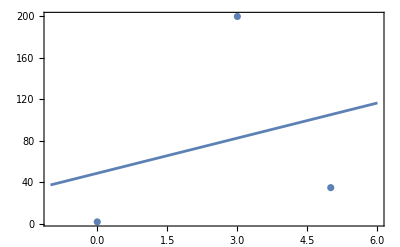

| Estimate | Standard Error | t-Statistic | P-Value
a | 11.2895 | 40.612 | 0.277983 | 0.827388
b | 48.8947 | 136.72 | 0.357626 | 0.781352

```mathematica
moderu = a x + b;
datass = {{0, 2}, {3, 200}, {5, 35}};
fiteado = NonlinearModelFit[datass, moderu, {a, b}, x];
Show[Plot[fiteado[x], {x, -1, 6}], ListPlot[datass], PlotRange->All, Frame->True]

fiteado["ParameterTable"]
```